# IPPT Model

## 2. Single Case Solver

Instructions:
- This notebook will evaluate the model using a single set of input conditions

How to Run:
- Define the input conditions you desire
- Click “Evaluate Notebook in Menu Options”
- Only the time-to-solution will be output explicitly, use “3. Single Case Plots” to visualize model results

## Inputs

Notes:
- Inputs loaded from csv file with name “DataIO-Run#.csv”
- Evaluate first cell then click “Browse...” button below to find csv file

```mathematica
Clear[DataIOFile]
FileNameSetter[Dynamic[DataIOFile],"OpenList"]
```

$CellContext`DataIOFileOpenListAll

```mathematica
(** Evaluate this to load csv file data **)
MasterTable=Import[DataIOFile[[1]]];
Nsols=Dimensions[MasterTable][[1]]-1

(** Generate Tables of Data from MasterTable **)

zmaxT=MasterTable[[2;;Nsols+1,1]];
zstepsT=MasterTable[[2;;Nsols+1,2]];
tmaxT=MasterTable[[2;;Nsols+1,3]];
tstepsT=MasterTable[[2;;Nsols+1,4]];
zs0T=MasterTable[[2;;Nsols+1,5]];
ws0T=MasterTable[[2;;Nsols+1,6]];
nn0T=MasterTable[[2;;Nsols+1,7]];
χi0T=MasterTable[[2;;Nsols+1,8]];
zχiT=MasterTable[[2;;Nsols+1,9]];
Te0T=MasterTable[[2;;Nsols+1,10]];
Ti0T=MasterTable[[2;;Nsols+1,11]];
znT=MasterTable[[2;;Nsols+1,12]];
LcT=MasterTable[[2;;Nsols+1,13]];
L0T=MasterTable[[2;;Nsols+1,14]];
RcT=MasterTable[[2;;Nsols+1,15]];
C0T=MasterTable[[2;;Nsols+1,16]];
V0T=MasterTable[[2;;Nsols+1,17]];
zcT=MasterTable[[2;;Nsols+1,18]];
routT=MasterTable[[2;;Nsols+1,19]];
rinT=MasterTable[[2;;Nsols+1,20]];
zc0T=MasterTable[[2;;Nsols+1,21]];
vsfT=MasterTable[[2;;Nsols+1,22]];
wsfT=MasterTable[[2;;Nsols+1,23]];
nsfT=MasterTable[[2;;Nsols+1,24]];
TefT=MasterTable[[2;;Nsols+1,25]];
nffT=MasterTable[[2;;Nsols+1,26]];
vffT=MasterTable[[2;;Nsols+1,27]];
mbitT=MasterTable[[2;;Nsols+1,28]];
IbitT=MasterTable[[2;;Nsols+1,29]];
IspT=MasterTable[[2;;Nsols+1,30]];
ηTT=MasterTable[[2;;Nsols+1,31]];
ηTrecT=MasterTable[[2;;Nsols+1,32]];
ηmT=MasterTable[[2;;Nsols+1,33]];
MassFracT=MasterTable[[2;;Nsols+1,34]];

(** Create Tables of Other Relevant Parameters **)

ΠionT=Table[nn0T[[j]] χi0T[[j]] Sion[Te0T[[j]]] (L0T[[j]] C0T[[j]])^(1/2),{j,1,Nsols}];
ΩionT=Table[1/(mbitT[[j]] ec ϵion[Te0T[[j]]]/mi)(1/2) C0T[[j]] V0T[[j]]^2(Rp[L0T[[j]],C0T[[j]],nn0T[[j]] ,nn0T[[j]],Te0T[[j]],ws0T[[j]],routT[[j]],rinT[[j]]]/L0T[[j]])π(C0T[[j]] L0T[[j]])^(1/2),{j,1,Nsols}];
νT=Table[(C0T[[j]](V0T[[j]])^2)/(mbitT[[j]](zcT[[j]]/((LcT[[j]]C0T[[j]])^(1/2)))^2),{j,1,Nsols}];
```

266

## Single Plots

Notes:
-Plots a single variable X vs Y
-Generates a table of X and table of Y composed of different j solutions

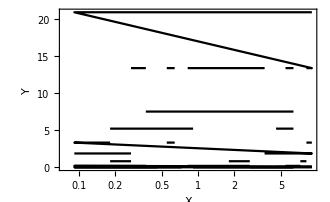

```mathematica
X=Table[ΠionT[[j]],{j,1,Nsols}];
Y=Table[ΩionT[[j]],{j,1,Nsols}];
LogLinearMultiCasePlot[X,Y,Automatic,Automatic,"X","Y"]
```

## Contour Plots

Notes:
-Generates contour plot of variable Z vs. X and Y
-Generates a table of X and table of Y composed of different j solutions

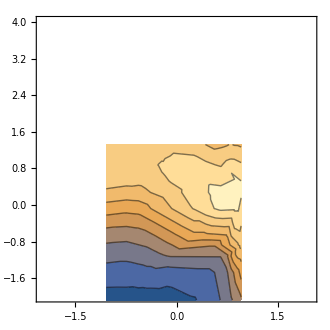

```mathematica
X=Table[Log[10,ΠionT[[j]]],{j,1,Nsols}];
Y=Table[Log[10,ΩionT[[j]]],{j,1,Nsols}];
Z=Table[ηmT[[j]],{j,1,Nsols}];
ListContourPlot[Table[{X[[j]],Y[[j]],Z[[j]]},{j,1,Nsols}],PlotRange->{{-2,2},{-2,4}}]
```

```mathematica
ΩionT
```

{0.117514,0.117514,0.117514,0.117514,0.117514,0.117514,0.117514,0.117514,0.117514,0.117514,0.117514,0.117514,0.117514,0.117514,0.117514,0.117514,0.117514,0.117514,0.117514,0.470056,0.470056,0.470056,0.470056,0.470056,0.470056,0.470056,0.470056,0.470056,0.470056,0.470056,0.470056,0.470056,0.470056,0.470056,0.470056,0.470056,0.470056,0.470056,1.05763,1.05763,1.05763,1.05763,1.05763,1.05763,1.05763,1.05763,1.05763,1.05763,1.05763,1.05763,1.05763,1.05763,1.05763,1.05763,1.05763,1.05763,1.05763,1.88022,1.88022,1.88022,1.88022,1.88022,1.88022,1.88022,1.88022,1.88022,1.88022,1.88022,1.88022,1.88022,1.88022,1.88022,1.88022,1.88022,1.88022,1.88022,2.9445,2.9445,2.9445,2.9445,2.9445,2.9445,2.9445,2.9445,2.9445,2.9445,2.9445,2.9445,2.9445,2.9445,2.9445,2.9445,2.9445,2.9445,2.9445,11.778,11.778,11.778,11.778,11.778,11.778,11.778,11.778,11.778,11.778,11.778,11.778,11.778,11.778,11.778,11.778,11.778,11.778,11.778,26.5005,26.5005,26.5005,26.5005,26.5005,26.5005,26.5005,26.5005,26.5005,26.5005,26.5005,26.5005,26.5005,26.5005,26.5005,26.5005,26.5005,26.5005,26.5005,47.112,47.112,47.112,47.112,47.112,47.112,47.112,47.112,47.112,47.112,47.112,47.112,47.112,47.112,47.112,47.112,47.112,47.112,47.112,73.6124,73.6124,73.6124,73.6124,73.6124,73.6124,73.6124,73.6124,73.6124,73.6124,73.6124,73.6124,73.6124,73.6124,73.6124,73.6124,73.6124,73.6124,73.6124,106.002,106.002,106.002,106.002,106.002,106.002,106.002,106.002,106.002,106.002,106.002,106.002,106.002,106.002,106.002,106.002,106.002,106.002,106.002,188.022,188.022,188.022,188.022,188.022,188.022,188.022,188.022,188.022,188.022,188.022,188.022,188.022,188.022,188.022,188.022,188.022,188.022,188.022,293.785,293.785,293.785,293.785,293.785,293.785,293.785,293.785,293.785,293.785,293.785,293.785,293.785,293.785,293.785,293.785,293.785,293.785,293.785,661.016,661.016,661.016,661.016,661.016,661.016,661.016,661.016,661.016,661.016,661.016,661.016,661.016,661.016,661.016,661.016,661.016,661.016,661.016,1175.14,1175.14,1175.14,1175.14,1175.14,1175.14,1175.14,1175.14,1175.14,1175.14,1175.14,1175.14,1175.14,1175.14,1175.14,1175.14,1175.14,1175.14,1175.14}

```mathematica
N[Log[10,105(100000/30000)^2]]
```

3.06695

```mathematica
N[Log[10,105(1000/30000)^2]]
```

-0.933053